## SSS1. Mathematica Basics

## Table of Contents

A. Mathematica Basics
	Data Types
		The structure of Mathematica
		Strings
		Booleans
		Numbers
		Lists
		Variables
	Functions
B. Topics

Welcome to your first Mathematica Structured Study Session. Just as you did for Python last semester, we want to give you a space and material to help you gain essential skills relevant to your courses and practice them.
The notebooks are divided into three sections: Lab(A), Topic(B) and Exercises(C). The lab will introduce new Mathematica concepts and have examples, that will help you figure out the exercises yourself. The Topic section will

The tutorials will assume you know the python from last semester decently well and make reference to python to help you understand the differences and learn Mathematica more quickly.
We will try to strike a mix between teaching the basics and

## A. Mathematica Basics

### Data Types

Maybe you remember from python that it is an object-oriented programming language that has various data types/object types, like Strings, Numbers, Lists, etc.

Mathematica does also have strings, numbers, lists, and many of the same types, but very importantly it is not an object-oriented programming language. If you go down to the source-code you will only find a few “atomic”(non-reducible) types: numbers (split into a few different types like Integers or Reals), strings, and symbols (which can be a lot of things). All of them are expressions and can be combined into new Expressions to make incredibly intricate data structures.

#### The structure of Mathematica

Empty lists and empty associations are not symbols: List[] (not a symbol), List (a symbol)

-Expressions
	- Numbers
		- Integers
		-Reals
	- Strings
	-symbols
		- empty Lists
		- empty Associations (aka Dictionaries)
		- Booleans
		- +, -, /, *,<,>
		-variables
		-...
	-image
	-graphs
	-combinations of numbers, strings, symbols,....
	-functions

Let’s look at a small example:
To display what a random mathematical expression looks like for Mathematica actually you can use the function FullForm

maybe”internally” instead of “actually”

FullForm of a mathematical expression:

```mathematica
FullForm[x^2+(y √2)/4-6*y]
```

Plus[Power[x,2],Times[-6,y],Times[Rational[1,2],Power[2,Rational[-1,2]],y]]

It is hard to see what’s going on just using times, but luckily there is a function that does the same thing displayed in a nicer way (just using times?)

TreeForm of mathematical expression

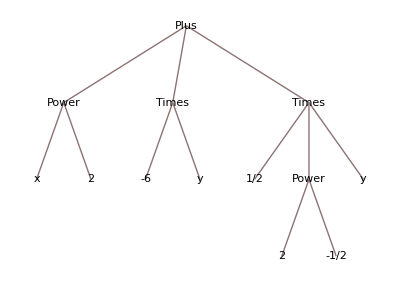

```mathematica
TreeForm[x^2+(y √2)/4-6*y]
```

You can see how the expression is internally broken up into the atomic pieces of numbers (like 2 or -6) and symbols (y or x). They are then combined by other symbols like Plus, Power or Times.
Try typing an expression yourself and look at the FullForm or TreeForm.

```mathematica
(*your code goes here*)
```

If you are more curious about how everything can be an expression, try the “Everything is an Expression”-Tutorial in the official documentation.
For practical purposes we will explore some of the expressions in more detail

that link is very fancy but unfortunately doesn’t work

#### Strings

Just as in python, strings are marked with quotes. Mathematica will automatically print everything, unless you follow it with a semicolon.

The classic Hello World Program

```mathematica
"Hello World"
```

Hello World

Don’t print the string by putting a semicolon

```mathematica
"Hello World";
```

#### Booleans

Boolean values are True or False values. They can be used as conditions, or returned by functions among many other things.
An example is many functions ending in Q. These are usually true or false questions.

```mathematica
EvenQ[5]
PrimeQ[137]
14≤12
1≠2
```

False

True

False

True

Might be more clear in seperate cells

#### Numbers

If you use one type of number like a fraction or an integer, Mathematica will try to return the answer in the same format

A simple multiplication

```mathematica
1/5*2x
```

(2 x)/5

The same multiplication as a fraction

```mathematica
0.2*2x
```

0.4 x

#### Lists

Mathematica lists can contain any type you want mixed together and can have as many dimensions as you want. They are described by curly brackets {} and can be indexed by double square brackets [[]]. It is indexed from 1, not 0 like python

Create a list of various types

```mathematica
aList={4,1,5,"Hello",a,b};
```

Access the first element in the list

```mathematica
aList[[1]]
```

4

You can give a list of indexes you want to access.

```mathematica
aList[[{2,4}]]
```

{1,Hello}

Notice that you did not assign a value to the variables a and b, but Mathematica did not throw an error. It will simply wait until you assign them a value and treat them as unassigned variables until then. This is incredibly useful when doing math.

Maybe mention ranges too (1;;2, etc like in python?)

#### Variables

Just as in python, you will use variables in your program. The convention for naming variables is capitalizing each new word without underscores or spaces, with the first word not capitalized (that is reserved for built-in functions)

```mathematica
aNumber=100;
aString="The number is:";
```

```mathematica
aString
aNumber
```

The number is:

100

### Functions

Mathematica’s syntax for functions is as follows:

```mathematica
function[input_,moreInputs_]:=operation[input,moreInputs]
```

Let’s look at an example

```mathematica
sumOfSquares[int1_,int2_]:=int1^2+int2^2
```

```mathematica
sumOfSquares[4,5]
```

41

Once it is defined you can also use this function inside of other functions

```mathematica
rootMeanSquare[int1_,int2_]:= sumOfSquares[int1,int2]^0.5
```

```mathematica
rootMeanSquare[41,52]
```

66.2193

For many things you will be using built-in functions, but you should keep in mind how to define your own.

## B. Topics

### Boolean Logic

You may remember the logic unit from last semester Formal Analysis. Mathematica can help you with things like making truth tables.

#### Notation

You can use the programming notation for the operators of && for AND, || for OR, ...
Or you can use the mathematical symbols by typing [esc]not[esc], for example, you would get ¬.
Below is a table with the different notation and what to type.

Logical Operator | programming  | x in [esc]x[esc] | displayed in formula
AND | && | and | ∧
(inclusive)OR | || | or | ∨
(exclusive) OR | NA | xor | ⊻
NOT | ! | not | ¬
NAND (NOTAND) | !&& | nand | ⊼
IMPLIES | NA | => | ⇒
You can now write things like 
(¬p ∧ q) ⊻ r

#### Evaluation & Simplification

After a boolean expression, you can

```mathematica
FullSimplify[(¬p∧q)⊻r ]
```

(!p&&q)⊻(r||p)

#### Examples

Let’s look

## C. Exercises